## Equations in terms of χ

```mathematica
(*
Subscript[χ, inc] = Cos[π/4];
RI = KerrGeoISSO[a,Subscript[χ, inc]];
L = KerrGeoAngularMomentum[a,KerrGeoISSO[a,Subscript[χ, inc]],0,Subscript[χ, inc] ];
Q = KerrGeoCarterConstant[a,KerrGeoISSO[a,Subscript[χ, inc]],0,Subscript[χ, inc] ];
ϵ =KerrGeoEnergy[a, KerrGeoISSO[a,Subscript[χ, inc]],0,Subscript[χ, inc] ];*)
```

```mathematica
(*Subscript[χ, inc] = Cos[π/4.37];
M=1
a = 0.689;

RI= KerrGeoISSO[a,Subscript[χ, inc]];
RM = M- Sqrt[M^2-a^2];
RP = M+ Sqrt[M^2-a^2];

Q=-M(RI)^(5/2)((Sqrt[(RI-RP)(RI-RM)]-2Sqrt[RI])^2-4 a^2)/(4 a^2(RI^(3/2)-Sqrt[RI]-Sqrt[(RI-RP)(RI-RM)]))
Qbh = KerrGeoCarterConstant[a,KerrGeoISSO[a,Subscript[χ, inc]],0,Subscript[χ, inc] ]
ϵ =(√(a^2 Q-2 M RI^3+3 RI^4))/(√3 RI^2)
ϵbh =KerrGeoEnergy[a, KerrGeoISSO[a,Subscript[χ, inc]],0,Subscript[χ, inc] ]


L1=(√(3 a^2 Q-a^2 RI^2-Q RI^2+3 RI^4+a^2 RI^2 ϵ^2-3 RI^4 ϵ^2))/RI

Lbh= KerrGeoAngularMomentum[a,KerrGeoISSO[a,ang ],0,ang  ]

Plot[{Re[L1[R]],Im[L1[R]]},{R,0,30}];
Plot[{Re[Q[R]],Im[Q[R]]},{R,0,30}];
Plot[{Re[ϵ[R]],Im[ϵ[R]]},{R,0,30}];
```

```mathematica
(*Subscript[χ, inc] = Cos[π/4.37];*)
(*RI= KerrGeoISSO[a,Subscript[χ, inc]];*)
(*Gam = RI^5-Q(RI-3)RI^3+a^2 Q^2;
ϵ= (RI^3(RI-2)-a(a Q+Sqrt[Gam ]))/(RI^2 Sqrt[RI^3(RI-3)-2a(a Q+Sqrt[Gam ])])*)
(*L =- (2 a RI^3+(RI^2+a^2)(a Q +Sqrt[Gam]))/(RI^2 Sqrt[RI^3(RI-3)-2a(a Q+Sqrt[Gam ])])*)
 (*Sqrt[(-a^2-L^2-Q+a^2 ϵ^2-√(12 a^2 Q (-3+3 ϵ^2)+(a^2+L^2+Q-a^2 ϵ^2)^2))/(6 (-1+ϵ^2))]*)

(*D[- M(RI)^(5/2)((Sqrt[(RI-RP)(RI-RM)]-2Sqrt[RI])^2-4 a^2)/(4 a^2(RI^(3/2)-Sqrt[RI]-Sqrt[(RI-RP)(RI-RM)])),RI]
-(5 M RI^(3/2) (-4 a^2+(-2 √RI+√((RI-RM) (RI-RP)))^2))/(8 a^2 (-√RI+RI^(3/2)-√((RI-RM) (RI-RP))))+(M RI^(5/2) (-4 a^2+(-2 √RI+√((RI-RM) (RI-RP)))^2) (-1/(2 √RI)+(3 √RI)/2-(2 RI-RM-RP)/(2 √((RI-RM) (RI-RP)))))/(4 a^2 (-√RI+RI^(3/2)-√((RI-RM) (RI-RP)))^2)-(M RI^(5/2) (-2 √RI+√((RI-RM) (RI-RP))) (-1/(√RI)+(2 RI-RM-RP)/(2 √((RI-RM) (RI-RP)))))/(2 a^2 (-√RI+RI^(3/2)-√((RI-RM) (RI-RP))))
Simplify[D[Sqrt[-a^2 x^2+2 x^3+(a^2 (-2 x^3+3 x^4-(M x^(5/2) (-4 a^2+(-2 Sqrt[x]+Sqrt[(x-RM) (x-RP)])^2))/(4 (-Sqrt[x]+x^(3/2)-Sqrt[(x-RM) (x-RP)]))))/(3 x^2)-(M x^(5/2) (-4 a^2+(-2 Sqrt[x]+Sqrt[(x-RM) (x-RP)])^2))/(2 (-Sqrt[x]+x^(3/2)-Sqrt[(x-RM) (x-RP)]))+(M x^(9/2) (-4 a^2+(-2 Sqrt[x]+Sqrt[(x-RM) (x-RP)])^2))/(4 a^2 (-Sqrt[x]+x^(3/2)-Sqrt[(x-RM) (x-RP)]))]/x,x]]
-1/(2 √3 x^2)(√(-1/(a^2 (√((RM-x) (RP-x))+√x-x^(3/2)))√x (4 a^6 M+3 M x^4 (RM (RP-x)-4 √((RM-x) (RP-x)) √x-(-4+RP) x+x^2)-6 a^2 x^2 (4 (√((RM-x) (RP-x)) √x+x-x^2)+M (RM (RP-x)-4 √((RM-x) (RP-x)) √x+4 x-RP x+3 x^2))+a^4 (8 (√((RM-x) (RP-x)) √x+x-x^2)+M (4 √((RM-x) (RP-x)) √x+(-4+RP) x+23 x^2+RM (-RP+x))))))+(-48 a^2 x+144 x^2+(6 M (-4 a^2+(√((RM-x) (RP-x))-2 √x)^2) ((RM+RP-2 x)/(√((RM-x) (RP-x)))-1/(√x)+3 √x) x^(5/2))/((√((RM-x) (RP-x))+√x-x^(3/2))^2)-(3 M (-4 a^2+(√((RM-x) (RP-x))-2 √x)^2) ((RM+RP-2 x)/(√((RM-x) (RP-x)))-1/(√x)+3 √x) x^(9/2))/(a^2 (√((RM-x) (RP-x))+√x-x^(3/2))^2)+(30 M (-4 a^2+(√((RM-x) (RP-x))-2 √x)^2) x^(3/2))/(√((RM-x) (RP-x))+√x-x^(3/2))-(27 M (-4 a^2+(√((RM-x) (RP-x))-2 √x)^2) x^(7/2))/(a^2 (√((RM-x) (RP-x))+√x-x^(3/2)))+(24 M (√((RM-x) (RP-x))-2 √x) x^(5/2) (-1/(√x)+(-RM-RP+2 x)/(2 √((-RM+x) (-RP+x)))))/(√((RM-x) (RP-x))+√x-x^(3/2))-(12 M (√((RM-x) (RP-x))-2 √x) x^(9/2) (-1/(√x)+(-RM-RP+2 x)/(2 √((-RM+x) (-RP+x)))))/(a^2 (√((RM-x) (RP-x))+√x-x^(3/2)))+4 a^2 (8-12 x-(M (-4 a^2+(√((RM-x) (RP-x))-2 √x)^2))/(√x (√((RM-x) (RP-x))+√x-x^(3/2))))+1/(√x)a^2 (-48 √x+96 x^(3/2)+(M (-4 a^2+(√((RM-x) (RP-x))-2 √x)^2) ((RM+RP-2 x)/(√((RM-x) (RP-x)))-1/(√x)+3 √x) x)/((√((RM-x) (RP-x))+√x-x^(3/2))^2)+(5 M (-4 a^2+(√((RM-x) (RP-x))-2 √x)^2))/(√((RM-x) (RP-x))+√x-x^(3/2))+(4 M (√((RM-x) (RP-x))-2 √x) x (-1/(√x)+(-RM-RP+2 x)/(2 √((-RM+x) (-RP+x)))))/(√((RM-x) (RP-x))+√x-x^(3/2))))/(8 √3 x √(-1/(a^2 (√((RM-x) (RP-x))+√x-x^(3/2)))√x (4 a^6 M+3 M x^4 (RM (RP-x)-4 √((RM-x) (RP-x)) √x-(-4+RP) x+x^2)-6 a^2 x^2 (4 (√((RM-x) (RP-x)) √x+x-x^2)+M (RM (RP-x)-4 √((RM-x) (RP-x)) √x+4 x-RP x+3 x^2))+a^4 (8 (√((RM-x) (RP-x)) √x+x-x^2)+M (4 √((RM-x) (RP-x)) √x+(-4+RP) x+23 x^2+RM (-RP+x))))))


Q =- M(RI)^(5/2)((Sqrt[(RI-RP)(RI-RM)]-2Sqrt[RI])^2-4 a^2)/(4 a^2(RI^(3/2)-Sqrt[RI]-Sqrt[(RI-RP)(RI-RM)]));


DLDRI[x_] :=-1/(2 √3 x^2)(√(-1/(a^2 (√((RM-x) (RP-x))+√x-x^(3/2)))√x (4 a^6 M+3 M x^4 (RM (RP-x)-4 √((RM-x) (RP-x)) √x-(-4+RP) x+x^2)-6 a^2 x^2 (4 (√((RM-x) (RP-x)) √x+x-x^2)+M (RM (RP-x)-4 √((RM-x) (RP-x)) √x+4 x-RP x+3 x^2))+a^4 (8 (√((RM-x) (RP-x)) √x+x-x^2)+M (4 √((RM-x) (RP-x)) √x+(-4+RP) x+23 x^2+RM (-RP+x))))))+(-48 a^2 x+144 x^2+(6 M (-4 a^2+(√((RM-x) (RP-x))-2 √x)^2) ((RM+RP-2 x)/(√((RM-x) (RP-x)))-1/(√x)+3 √x) x^(5/2))/((√((RM-x) (RP-x))+√x-x^(3/2))^2)-(3 M (-4 a^2+(√((RM-x) (RP-x))-2 √x)^2) ((RM+RP-2 x)/(√((RM-x) (RP-x)))-1/(√x)+3 √x) x^(9/2))/(a^2 (√((RM-x) (RP-x))+√x-x^(3/2))^2)+(30 M (-4 a^2+(√((RM-x) (RP-x))-2 √x)^2) x^(3/2))/(√((RM-x) (RP-x))+√x-x^(3/2))-(27 M (-4 a^2+(√((RM-x) (RP-x))-2 √x)^2) x^(7/2))/(a^2 (√((RM-x) (RP-x))+√x-x^(3/2)))+(24 M (√((RM-x) (RP-x))-2 √x) x^(5/2) (-1/(√x)+(-RM-RP+2 x)/(2 √((-RM+x) (-RP+x)))))/(√((RM-x) (RP-x))+√x-x^(3/2))-(12 M (√((RM-x) (RP-x))-2 √x) x^(9/2) (-1/(√x)+(-RM-RP+2 x)/(2 √((-RM+x) (-RP+x)))))/(a^2 (√((RM-x) (RP-x))+√x-x^(3/2)))+4 a^2 (8-12 x-(M (-4 a^2+(√((RM-x) (RP-x))-2 √x)^2))/(√x (√((RM-x) (RP-x))+√x-x^(3/2))))+1/(√x)a^2 (-48 √x+96 x^(3/2)+(M (-4 a^2+(√((RM-x) (RP-x))-2 √x)^2) ((RM+RP-2 x)/(√((RM-x) (RP-x)))-1/(√x)+3 √x) x)/((√((RM-x) (RP-x))+√x-x^(3/2))^2)+(5 M (-4 a^2+(√((RM-x) (RP-x))-2 √x)^2))/(√((RM-x) (RP-x))+√x-x^(3/2))+(4 M (√((RM-x) (RP-x))-2 √x) x (-1/(√x)+(-RM-RP+2 x)/(2 √((-RM+x) (-RP+x)))))/(√((RM-x) (RP-x))+√x-x^(3/2))))/(8 √3 x √(-1/(a^2 (√((RM-x) (RP-x))+√x-x^(3/2)))√x (4 a^6 M+3 M x^4 (RM (RP-x)-4 √((RM-x) (RP-x)) √x-(-4+RP) x+x^2)-6 a^2 x^2 (4 (√((RM-x) (RP-x)) √x+x-x^2)+M (RM (RP-x)-4 √((RM-x) (RP-x)) √x+4 x-RP x+3 x^2))+a^4 (8 (√((RM-x) (RP-x)) √x+x-x^2)+M (4 √((RM-x) (RP-x)) √x+(-4+RP) x+23 x^2+RM (-RP+x))))));


ϵ=(√(a^2 Q-2 RI^3+3 RI^4))/(√3 RI^2);
J = 1-ϵ^2;

L[RI_]:=Piecewise[{{(√(-Q RI^2+3 J RI^4+a^2 (3 Q+RI^2 (-1+ϵ^2))))/RI,DLDRI[RI] < 0},{(-√(-Q RI^2+3 J RI^4+a^2 (3 Q+RI^2 (-1+ϵ^2))))/RI, DLDRI[RI] >=0}}];
Plot[- M(RI)^(5/2)((Sqrt[(RI-RP)(RI-RM)]-2Sqrt[RI])^2-4 a^2)/(4 a^2(RI^(3/2)-Sqrt[RI]-Sqrt[(RI-RP)(RI-RM)])),{RI,RISSOMIN,RISSOMAX}]
Plot[DLDRI[RI] ,{RI,RISSOMIN,RISSOMAX}]

Plot[L[RI], {RI,RISSOMIN,RISSOMAX}]*)
```

## Setting Up Equations

```mathematica
Clear["Global`*"]
```

## Solving for RISSOMIN and RISSOPLUS

## Range check for possible ISSO’s

```mathematica
a = 0.9`50;
M = 1;
RM = M- Sqrt[M^2-a^2];
RP = M+ Sqrt[M^2-a^2];
DN = (27-45 a^2+17 a^4+a^6+8 a^3 (1-a^2))^(1/3);
{RISSOMIN,RISSOMAX  }={ 3+√(3+a^2+(9-10 a^2+a^4)/DN+DN)-1/2 √(72+8 (-6+a^2)-(4 (9-10 a^2+a^4))/DN-4 DN+(64 a^2)/(√(3+a^2+(9-10 a^2+a^4)/DN+DN))),3+√(3+a^2+(9-10 a^2+a^4)/DN+DN)+1/2 √(72+8 (-6+a^2)-(4 (9-10 a^2+a^4))/DN-4 DN+(64 a^2)/(√(3+a^2+(9-10 a^2+a^4)/DN+DN)))}
```

{2.320883041761887246790086191922686088978602324769,8.717352279606489315950123122494743547431077684614}

### Param by Inclination

```mathematica
<<KerrGeodesics`
Subscript[χ, inc] = Cos[π/4];
RI = KerrGeoISSO[a,Subscript[χ, inc]]
ϵ =KerrGeoEnergy[a, KerrGeoISSO[a,Subscript[χ, inc]],0,Subscript[χ, inc] ]
L = KerrGeoAngularMomentum[a,KerrGeoISSO[a,Subscript[χ, inc]],0,Subscript[χ, inc] ]
Q = KerrGeoCarterConstant[a,KerrGeoISSO[a,Subscript[χ, inc]],0,Subscript[χ, inc] ]


J = 1-ϵ^2;
R4 =(a^2 Q)/(J*RI^3) ;
Rmid = (RI+RP)/2;
Z1=Sqrt[1/2 (1+(L^2+Q)/(a^2 (1-ϵ^2))-√(-(4 Q)/(a^2 (1-ϵ^2))+(-1-(L^2+Q)/(a^2 (1-ϵ^2)))^2))];
Z2 =Sqrt[ (a^2(1-ϵ^2))/2 (1+(L^2+Q)/(a^2 (1-ϵ^2))+√(-(4 Q)/(a^2 (1-ϵ^2))+(-1-(L^2+Q)/(a^2 (1-ϵ^2)))^2))];
KZ = a^2*J(Z1^2/Z2^2);

λzΛ = (4 EllipticK[KZ])/Z2;
Q =- M(RI)^(5/2)((Sqrt[(RI-RP)(RI-RM)]-2Sqrt[RI])^2-4 a^2)/(4 a^2(RI^(3/2)-Sqrt[RI]-Sqrt[(RI-RP)(RI-RM)]));
ϵ=(√(a^2 Q-2 RI^3+3 RI^4))/(√3 RI^2);
J = 1-ϵ^2;
```

3.06482214349668698406957806664055419737808876833

0.89028148091153471659956078884420950237761428

1.79557639228147148202810634406527523546694517

3.30809112884066044202638715279067161952546367

### Param by RI

```mathematica
RI = 5.6`50;
Q =- M(RI)^(5/2)((Sqrt[(RI-RP)(RI-RM)]-2Sqrt[RI])^2-4 a^2)/(4 a^2(RI^(3/2)-Sqrt[RI]-Sqrt[(RI-RP)(RI-RM)]));
ϵ=(√(a^2 Q-2 RI^3+3 RI^4))/(√3 RI^2);
L=-(√(-Q RI^2+3 J RI^4+a^2 (3 Q+RI^2 (-1+ϵ^2))))/RI;

J = 1-ϵ^2;
R4 =(a^2 Q)/(J*RI^3) ;
Rmid = (RI+RP)/2;
Z1=Sqrt[1/2 (1+(L^2+Q)/(a^2 (1-ϵ^2))-√(-(4 Q)/(a^2 (1-ϵ^2))+(-1-(L^2+Q)/(a^2 (1-ϵ^2)))^2))];
Z2 =Sqrt[ (a^2(1-ϵ^2))/2 (1+(L^2+Q)/(a^2 (1-ϵ^2))+√(-(4 Q)/(a^2 (1-ϵ^2))+(-1-(L^2+Q)/(a^2 (1-ϵ^2)))^2))];
KZ = a^2*J(Z1^2/Z2^2);

λzΛ = (4 EllipticK[KZ])/Z2;
Q =- M(RI)^(5/2)((Sqrt[(RI-RP)(RI-RM)]-2Sqrt[RI])^2-4 a^2)/(4 a^2(RI^(3/2)-Sqrt[RI]-Sqrt[(RI-RP)(RI-RM)]));
ϵ=(√(a^2 Q-2 RI^3+3 RI^4))/(√3 RI^2);
J = 1-ϵ^2;
R4 =(a^2 Q)/(J*RI^3) ;
Rmid = (RI+RP)/2;
```

### Flow Rate

z[2.450542645404286313363371912321676038922251]

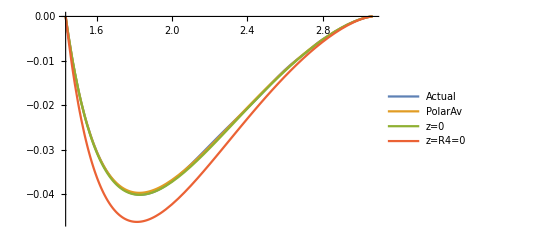

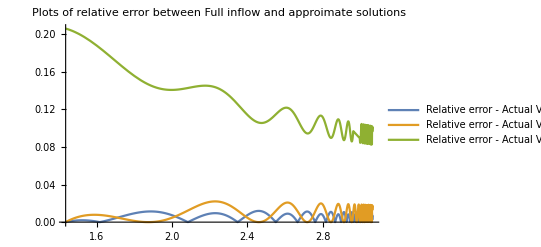

```mathematica
Λ = z[(4 EllipticK[KZ])/Z2]
R[r_]:= (ϵ(r^2+a^2)-a*L)^2-(r^2-2M*r+a^2)(r^2+(a*ϵ-L)^2+Q)
RadialInFlow[r_]:= (-Sqrt[R[r]])/(a L +(r^2+a^2)/((r-RP)(r-RM))(ϵ(r^2+a^2)-a L )-a^2 ϵ(1-(Z1 JacobiSN[ (2 Z2 √(r-R4))/(√(J (RI-r) (R4-RI)^2))+EllipticK[KZ],KZ])^2))

RadialInFlow2[r_]:= (-Sqrt[R[r]])/(a L +(r^2+a^2)/((r-RP)(r-RM))(ϵ(r^2+a^2)-a L )-a^2 ϵ + ( Z2^2/J(1-EllipticE[KZ]/EllipticK[KZ])  ))
RadialInFlow3[r_]:= (-Sqrt[(ϵ(r^2+a^2)-a*L)^2-(r^2-2M*r+a^2)(r^2+(a*ϵ-L)^2+Q)])/(a L +(r^2+a^2)/((r-RP)(r-RM))(ϵ(r^2+a^2)-a L )-a^2 ϵ)
RadialInFlow4[r_]:= (-Sqrt[J(RI-r)^3(r)])/(a L +(r^2+a^2)/((r-RP)(r-RM))(ϵ(r^2+a^2)-a L )-a^2 ϵ)
Plot[{RadialInFlow[r],RadialInFlow2[r],RadialInFlow3[r],RadialInFlow4[r]},{r,RP,RI}, PlotRange->All,PlotLegends->{"Actual","PolarAv","z=0","z=R4=0"}]
Plot[{Abs[(RadialInFlow[r] - RadialInFlow2[r])/RadialInFlow[r]] ,Abs[(RadialInFlow[r] - RadialInFlow3[r])/RadialInFlow[r]],Abs[(RadialInFlow[r] - RadialInFlow4[r])/RadialInFlow[r]] },{r,RP,RI-0.001}, PlotRange->All, PlotLabel->"Plots of relative error between Full inflow and approimate solutions",PlotLegends->{"Relative error - Actual Vs PolarAv","Relative error - Actual Vs z=0","Relative error - Actual Vs z=R4=0"}]
```

### Radial Equation

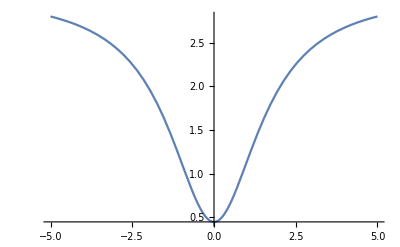

```mathematica
Mino[r_]:=(2 √(r-R4))/(√(J (RI-r) (R4-RI)^2));
r[λ_]:=((RI(RI-R4)^2 J*(λ)^2+4*R4)/((RI-R4)^2 J*(λ)^2+4));
Plot[r[λ],{λ,-5,5}]
```

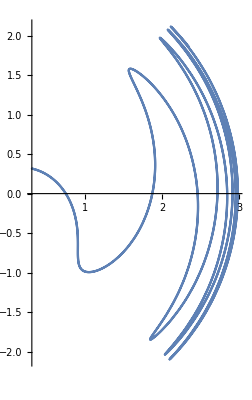

0.785398163397448309615660845819875721049292

```mathematica
ΥZ = (π*Z2)/(2*EllipticK[KZ]);
qZ[λ_]:= ΥZ*λ 
z[λ_] :=Z1*JacobiSN[Z2*(λ  ) + EllipticK[KZ],KZ];
θ[λ_] := ArcCos[Z1*JacobiSN[Z2*(λ )  + EllipticK[KZ] ,KZ]];
PolyZ[λ_] := (z[λ]^2-Z1^2)*(a^2(1-ϵ^2)z[λ]^2-Z2^2)
ParametricPlot[{r[λ]*Cos[π/2-θ[λ]],r[λ]*Sin[π/2-θ[λ]]} , {λ,-10,10}, PlotRange->All]

θ[0]
```

### Azimuthal Equation

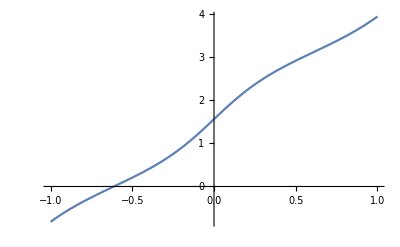

```mathematica
Υϕ =   L/EllipticK[KZ] EllipticPi[Z1^2, KZ];
qϕ[λ_] := Υϕ*λ + π/2;

Subscript[ϕ, r][λ_]:=1/(√J)2 a (((λ) (RI-R4)√J (-a L+a^2 ϵ+RI^2 ϵ))/(2(-R4+RI) (RI-RM) (RI-RP))+((-a L+a^2 ϵ+RM^2 ϵ) ArcTanh[(2  √(RM-R4))/((λ)  (RI-R4)√J √(RI-RM))])/(√(RM-R4) (RI-RM)^(3/2) (-RM+RP))+((-a L+a^2 ϵ+RP^2 ϵ) ArcTanh[(2  √(RP-R4))/((λ)  (RI-R4)√J √(RI-RP))])/(√(RP-R4) (RI-RP)^(3/2) (RM-RP)))    ;
Subscript[ϕ, θ][λ_] :=L/Z2 EllipticPi[Z1^2,JacobiAmplitude[Z2 (λ  )  + EllipticK[KZ],KZ],KZ];

ϕ[λ_] := Subscript[ϕ, r][λ]+ Subscript[ϕ, θ][λ] -a*ϵ*λ

Plot[Subscript[ϕ, θ][λ],{λ,-1,1}]
```

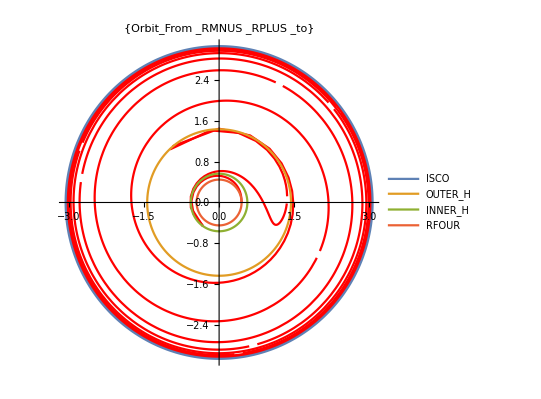

```mathematica
Q1 = ParametricPlot[{Re[r[λ]]*Sin[Re[ϕ[λ]]],Re[r[λ]]Cos[Re[ϕ[λ]]]}, {λ,0,20}, PlotRange->All, PlotLabel->{Orbit_From_RPLUS_to_RMNUS}, PlotStyle->Red, PlotLegends->ORBIT];
Q2 = ParametricPlot[{{RI*Cos[u],RI Sin[u]},{RP*Cos[u],RP Sin[u]},{RM*Cos[u],RM Sin[u]},{R4*Cos[u],R4 Sin[u]}},{u,-π,π},MaxRecursion->12,PlotRange->All,PlotLegends->{ISCO,OUTER_H,INNER_H,RFOUR}];

Show[Q1,Q2]
```

### 3D plots

### (*,Specularity[White,1000]*)

```mathematica
P1 = ParametricPlot3D[{Re[r[λ]]*Sin[Re[ϕ[λ]]]*Sin[Re[θ[λ]]],Re[r[λ]]*Sin[Re[θ[λ]]]*Cos[Re[ϕ[λ]]],Re[r[λ]]*Cos[Re[θ[λ]]]},{λ,0,10}, PlotStyle->Red,PlotRange->All];
P2 =ParametricPlot3D[{RP*Sin[u] Sin[v],RP*Cos[u] Sin[v],RP*Cos[v]},{u,-π,π},{v,-π,π},MaxRecursion->4,PlotStyle->{Opacity[1],Black,Specularity[White,10]}, Lighting->"Neutral",Axes->None,Mesh->None,PlotRange->All];
Show[P1,P2]
```

-Graphics3D-

### Time Function

#### Radial Part of time function

```mathematica
(*Clear[J,RI,R4,J,RM,RP]*)
```

```mathematica
Trr[λ_]:= ((a^2+RI^2) (-a L+(a^2+RI^2) ϵ)(λ))/((RI-RM) (RI-RP))+(2 (R4-RI)^2 ϵ (λ))/(4+J (R4-RI)^2 (λ)^2)-(R4+3 RI+2 (RM+RP))/Sqrt[J] ϵ ArcTan[((λ)  (RI-R4)√J)/2]+(2 (a^2+RM^2) (-a L+a^2 ϵ+RM^2 ϵ) ArcTanh[(2  √(RM-R4))/((λ)  (RI-R4)√J √(RI-RM))])/(√(RM-R4) (RI-RM)^(3/2) (-RM+RP)Sqrt[J])+(2 (a^2+RP^2) (-a L+a^2 ϵ+RP^2 ϵ) ArcTanh[(2  √(RP-R4))/((λ)  (RI-R4)√J √(RI-RP))])/(Sqrt[J] √(RP-R4) (RI-RP)^(3/2) (RM-RP));


(*TPolyR[λ_]:=  (r[λ]^2+a^2)/((r[λ]-RP)(r[λ]-RM))(ϵ(r[λ]^2+a^2)-a*L)
Plot[{Subscript[T, r]'[λ],TPolyR[λ],Subscript[T, r]'[λ]-TPolyR[λ] },{λ,-10,10},PlotLegends->{TPRIME,TPLOY,Diff}] - Must Change the branch we pick in negative time*)
```

#### ϕ part of time function

```mathematica
(*Clear["Global`*"]*)
```

```mathematica
(*tTildeϕ[ξ_] = -ϵ/(1-ϵ^2)Z2*EllipticE[ξ, KZ];*)

Tz[λ_]:=1/J ϵ  (-Z2 EllipticE[JacobiAmplitude[Z2 (λ  ) + EllipticK[KZ],KZ],KZ]+(Z2-a^2 J/Z2) EllipticF[JacobiAmplitude[Z2 (λ  ) + EllipticK[KZ],KZ],KZ])
T[λ_]:= Trr[λ]+Tz[λ]+a*L*λ
```

### Mino Time in terms of Proper Time

```mathematica
Simplify[Integrate[r^2/(Sqrt[J](RI-r)^(3/2)(r-R4)^(1/2)), r]];
```

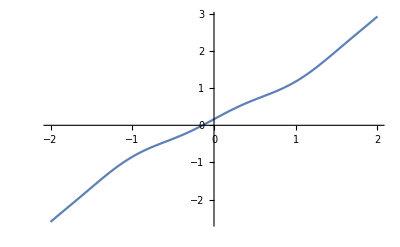

```mathematica
Subscript[τ, λr][λ_] :=(λ) (RI^2+(2(R4-RI)^2)/(4+J (R4-RI)^2(λ)^2))+((R4^2+2 R4 RI-3 RI^2) ArcTan[(λ)  (RI-R4)(√J)/2])/(√J (-R4+RI))
Subscript[τ, λz][λ_] :=1/J Z2  (-EllipticE[ JacobiAmplitude[Z2 (λ  ) + EllipticK[KZ],KZ],KZ]+EllipticF[JacobiAmplitude[Z2 (λ  ) + EllipticK[KZ],KZ],KZ])


τ[λ_]:= Subscript[τ, λz][λ]+Subscript[τ, λr][λ]

Plot[τ[λ],{λ,-2,2}]
```

### Small Q approximation

```mathematica
RIQ[Q_] :=Sqrt[ (-4-a^2-Q+a^2 ϵ^2-√(12 a^2 Q (-3+3 ϵ^2)+(4+a^2+Q-a^2 ϵ^2)^2))/(6 (-1+ϵ^2))]
```

### Kruskal Coordinates

```mathematica
σP = (M*RP)/Sqrt[M^2-a^2];
σM = (M*RM)/Sqrt[M^2-a^2];
ν = σM/σP;


V[λ_] := Abs[r[λ]-RP]^(1/2)/Abs[r[λ]-RM]^(ν/2)Exp[(r[λ]+T[λ])/(2 σP)];
U[λ_] := -Abs[r[λ]-RP]^(1/2)/Abs[r[λ]-RM]^(ν/2)Exp[(r[λ]-T[λ])/(2 σP)];
ParametricPlot[{Re[U[λ]],Re[V[λ]]},{λ,-3,3}];
```

```mathematica
Integrate[1/Sqrt[(r-R1)(r-R2)(r-R3)(r-R4)], r];
```

### Analysis

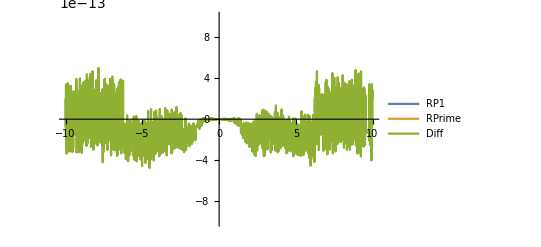

```mathematica
RPoly1[r_]:= (ϵ(r^2+a^2)-a*L)^2-(r^2-2M*r+a^2)(r^2+(a*ϵ-L)^2+Q)

Plot[{RPoly1[r[λ]], (r'[λ])^2, (r'[λ])^2- RPoly1[r[λ]]},{λ,-10,10}, PlotLegends->{RP1,RPrime,Diff},  PlotRange->{{-10,10},{-0.0000000000010,0.0000000000010}}]
```

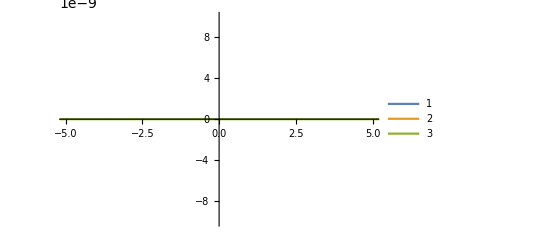

```mathematica
Polyθ[λ_] := (z[λ]^2-Z1^2)*(a^2(1-ϵ^2)z[λ]^2-Z2^2)
Plot[{(z'[λ])^2, Polyθ[λ], (z'[λ])^2- Polyθ[λ]}, {λ,-10,10}, PlotLegends->Automatic ,PlotLegends->{PolyθQ,θQ,θQ-PolyθQ}, PlotRange->{{-5,5},{-0.000000010,0.000000010}}]
```

```mathematica
|
```

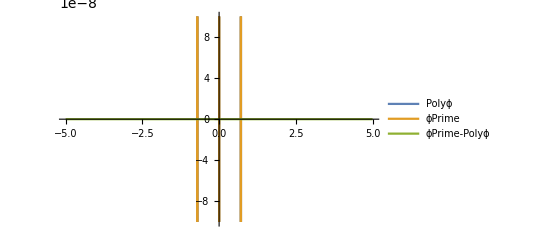

```mathematica
(*Plot[Im[ϕ[λ]],{λ,-5,5}]*)
Polyϕ[λ_]:= a/((r[λ]-RP)(r[λ]-RM))(ϵ(r[λ]^2+a^2)-a*L) + L/(1-z[λ]^2)-a*ϵ
Plot[{Polyϕ[λ],Re[ϕ'[λ]],Re[ϕ'[λ]-Polyϕ[λ]]},{λ,-5,5}, PlotRange->{{-5,5},{-0.00000010,0.00000010}},PlotLegends->{Polyϕ,ϕPrime,ϕPrime-Polyϕ}]
```

```mathematica
|
```

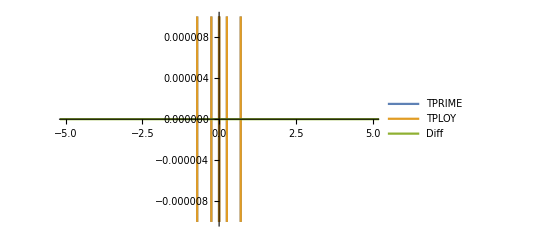

```mathematica
TPrime[λ_]:= Re[Piecewise[{{Subscript[T, r]'[λ]+Subscript[T, z]'[λ]+a*L,λ>0},{-Subscript[T, r]'[λ]+Subscript[T, z]'[λ]+a*L,λ<0}}]]
TPoly[λ_]:=  (r[λ]^2+a^2)/((r[λ]-RP)(r[λ]-RM))(ϵ(r[λ]^2+a^2)-a*L)-a^2 ϵ(1-z[λ]^2)+a*L
Plot[{Re[T'[λ]],TPoly[λ],Re[T'[λ]]-TPoly[λ] },{λ,-10,10},PlotLegends->{TPRIME,TPLOY,Diff}, PlotRange->{{-5,5},{-0.000010,0.000010}}]
```

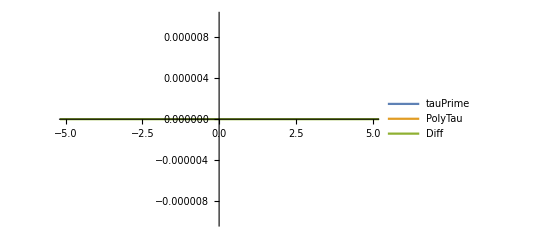

```mathematica
Plot[{τ'[λ],r[λ]^2+a^2 z[λ]^2,τ'[λ]-(r[λ]^2+a^2 z[λ]^2)},{λ,-10,20},{PlotLegends->{tauPrime,PolyTau,Diff}},PlotRange->{{-5,5},{-0.000010,0.000010}}]
```

### dr/dtAve

0.68493416641857854871463220142654835765383173

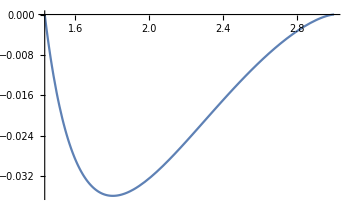

```mathematica
Λ = z[(4 EllipticK[KZ])/Z2]
R[r_]:= (ϵ(r^2+a^2)-a*L)^2-(r^2-2M*r+a^2)(r^2+(a*ϵ-L)^2+Q)
CoordTimeAveRadialInFlow[r_]:= (-Sqrt[R[r]])/(a L +(r^2+a^2)/((r-RP)(r-RM))(ϵ(r^2+a^2)-a L )-ϵ( Z2^2/J(1-EllipticE[KZ]/EllipticK[KZ])   -a^2 ))


Plot[CoordTimeAveRadialInFlow[r], {r,RI,RP}]
```

```mathematica
ϵ( Z2^2/J(1-EllipticE[KZ]/EllipticK[KZ])   -a^2 )
```

-0.308436150604425828280169123873477922579628

51.934630685060933415429254731571615276167966

### Finding L and ϵ in terms of RI

```mathematica
Collect[(ϵ(r^2+a^2)-a*L)^2-(r^2-2M*r+a^2)(r^2+(a*ϵ-L)^2+Q) - J(RI-r)^3(r-(a^2 Q)/(J*RI^3))==0,r]
```

```mathematica
+r^4 (-1+J+ϵ^2)+r^2 (-a^2-Q+(3 a^2 Q)/RI^2+3 J RI^2-2 a L ϵ+2 a^2 ϵ^2-(-L+a ϵ)^2)+r (2 M Q-(3 a^2 Q)/RI-J RI^3+2 M (-L+a ϵ)^2)==0
```

0.-6.75016×10^-14 r+2.60209×10^-16 r^2==0

```mathematica
Expand[-2 a^3 L ϵ+a^4 ϵ^2-a^2 (-L+a ϵ)^2+a^2 L^2]
```

0

```mathematica
Solve[2 M-(a^2 Q)/RI^3-3 (1-ϵ^2)RI==0,ϵ]
```

{{ϵ→-(√(a^2 Q-2 M RI^3+3 RI^4))/(√3 RI^2)},{ϵ→(√(a^2 Q-2 M RI^3+3 RI^4))/(√3 RI^2)}}

```mathematica
Simplify[Solve[-a^2-Q+(3 a^2 Q)/RI^2+3 J RI^2-2 a L ϵ+2 a^2 ϵ^2-(-L+a ϵ)^2==0,L]]
Simplify[Solve[2 M Q-(3 a^2 Q)/RI-J RI^3+2 M (-L+a ϵ)^2==0,L]]
```

```mathematica
{{L->-(√(-Q RI^2+3 J RI^4+a^2 (3 Q+RI^2 (-1+ϵ^2))))/RI},{L->(√(-Q RI^2+3 J RI^4+a^2 (3 Q+RI^2 (-1+ϵ^2))))/RI}}
{{L->-(√(M (3 a^2 Q-2 M Q RI+J RI^4)))/(√2 M √RI)+a ϵ},{L->(√(M (3 a^2 Q-2 M Q RI+J RI^4)))/(√2 M √RI)+a ϵ}}
```

{{L→-(√(M (3 a^2 Q-2 M Q RI+J RI^4)))/(√2 M √RI)+a ϵ},{L→(√(M (3 a^2 Q-2 M Q RI+J RI^4)))/(√2 M √RI)+a ϵ}}

```mathematica
Q =- M(RI)^(5/2)((Sqrt[(RI-RP)(RI-RM)]-2Sqrt[RI])^2-4 a^2)/(4 a^2(RI^(3/2)-Sqrt[RI]-Sqrt[(RI-RP)(RI-RM)]));


(√(-Q RI^2+3 J RI^4+a^2 (3 Q+RI^2 (-1+ϵ^2))))/RI
```

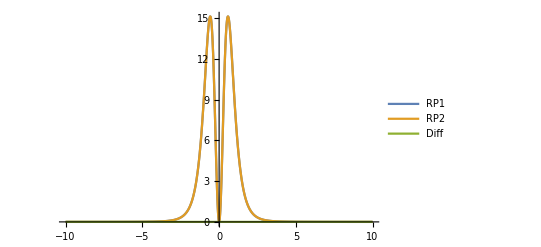

```mathematica
RPoly1[r_]:= (ϵ(r^2+a^2)-a*L)^2-(r^2-2M*r+a^2)(r^2+(a*ϵ-L)^2+Q)

RPoly2[r_]:=J(RI-r)^3(r-R4)

Polyphir[r_]:= (a(ϵ(r^2+a^2)-a*L))/((r-RM)(r-RP));
Plot[{RPoly1[r[λ]], RPoly2[r[λ]], RPoly1[r[λ]]- RPoly2[r[λ]]},{λ,-10,10}, PlotLegends->{RP1,RP2,Diff},  PlotRange->All]
```

### Conserved Quantities

6.243229588336492462782520728227149873495024634

4.719875456705250259606683219643208223348978997

-1.38515923310188171048053074210064767486857113

-1.385159233101881710480530742100647674869

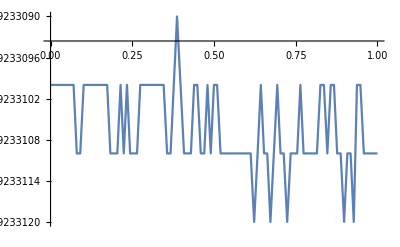

```mathematica
ENERGY[λ_]:= ((-1+(2 r[λ])/(r[λ]^2+a^2 z[λ]^2)) T'[λ])/(r[λ]^2+a^2 z[λ]^2)-(2 a r[λ] (1-z[λ]^2) ϕ'[λ])/((r[λ]^2+a^2 z[λ]^2) (r[λ]^2+a^2 z[λ]^2));
AngularMomentum[λ_]:= -(2 a r[λ] (1-z[λ]^2) T'[λ])/((r[λ]^2+a^2 z[λ]^2) (r[λ]^2+a^2 z[λ]^2))+((1-z[λ]^2) (2 a^2 r[λ] (1-z[λ]^2)+(a^2+r[λ]^2) (r[λ]^2+a^2 z[λ]^2)) ϕ'[λ])/((r[λ]^2+a^2 z[λ]^2) (r[λ]^2+a^2 z[λ]^2));
Mino[RP]
Mino[RM]
L
AngularMomentum[4]
Plot[Re[AngularMomentum[λ]],{λ,0, 1}, MaxRecursion->15, {PlotRange->All}]
```

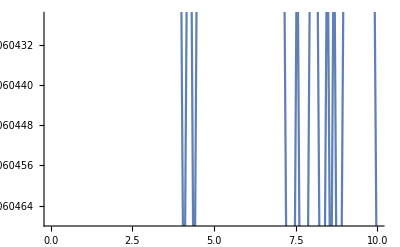

```mathematica
test[λ_]:=1/(J Z2)ϵ (Z2^2 EllipticE[JacobiAmplitude[Z2 λ+EllipticK[KZ],KZ],KZ]-Z2^2 EllipticE[JacobiAmplitude[Z2 λ+5 EllipticK[KZ],KZ],KZ]+(a^2 J-Z2^2) (EllipticF[JacobiAmplitude[Z2 λ+EllipticK[KZ],KZ],KZ]-EllipticF[JacobiAmplitude[Z2 λ+5 EllipticK[KZ],KZ],KZ]))
Plot[1/((4 EllipticK[KZ])/Z2)test[λ],{λ,0,10}]
```

```mathematica
(4 EllipticK[KZ])/Z2
```

1.764826278573841642114557883138536960106563323

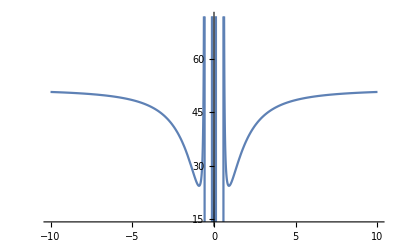

```mathematica
Test[λ_]:=(r[λ]^2+a^2)/((r[λ]-RP)(r[λ]-RM))(ϵ(r[λ]^2+a^2)-a*L)+a*L
Plot[Test[λ],{λ,-10,10}]
```

15.3873441140711686369299002838440063413562406

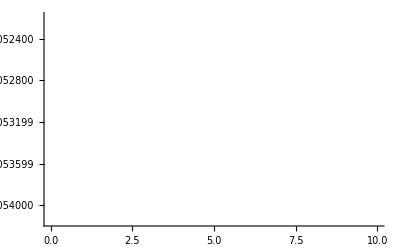

```mathematica
4EllipticK[KZ](1-(a^2 J)/Z2^2)1/(J Z2)ϵ
```

### F term

```mathematica
FDiff[λ_]:=1/J ϵ  ((Z2-a^2 J/Z2) EllipticF[JacobiAmplitude[Z2 (λ  ) + 5EllipticK[KZ],KZ],KZ])-1/J ϵ  ((Z2-a^2 J/Z2) EllipticF[JacobiAmplitude[Z2 (λ  ) + EllipticK[KZ],KZ],KZ])
Plot[FDiff[λ],{λ,0,10}]
FDiff[30] - Z2/J ϵ(4EllipticK[KZ](1-(a^2 J)/Z2^2))
```

-Graphics-

0.

```mathematica
JacobiAmplitude[DEL,KZ]
JacobiDN[DEL,KZ]
```

6.283185307179586476925286766559005768394338799

```mathematica
JacobiEpsilon[DEL,KZ]-2π
```

-0.02218810659915471366419850166578462489552243

```mathematica
JacobiEpsilon[DEL,KZ]
```

-0.02218810659915471366419850166578462489552243

```mathematica
1/J ϵ  (-Z2 );

Ediff[λ_]:=  ( EllipticE[JacobiAmplitude[Z2 (λ  ) + 5EllipticK[KZ],KZ],KZ]) -(EllipticE[JacobiAmplitude[Z2 (λ ) + EllipticK[KZ],KZ],KZ])
DEL=4 EllipticK[KZ];
JacobiEpsilon[DEL,KZ]-Ediff[10]
```

0.

```mathematica
DEL=100*4 EllipticK[KZ]/Z2;
```

-0.308436150604425828280169123873477922579628

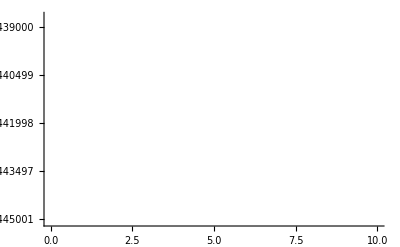

```mathematica
Totaldiff[λ_]:= 1/DEL(1/J ϵ  (-Z2 EllipticE[JacobiAmplitude[Z2 (λ +DEL ) + EllipticK[KZ],KZ],KZ]+(Z2-a^2 J/Z2) EllipticF[JacobiAmplitude[Z2 (λ+DEL  ) + EllipticK[KZ],KZ],KZ]) -1/J ϵ  (-Z2 EllipticE[JacobiAmplitude[Z2 (λ  ) + EllipticK[KZ],KZ],KZ]+(Z2-a^2 J/Z2) EllipticF[JacobiAmplitude[Z2 (λ  ) + EllipticK[KZ],KZ],KZ]))


Shift = ϵ Z2^2/J( 1-EllipticE[KZ]/EllipticK[KZ]  -a^2 J/Z2^2)

Plot[{Totaldiff[λ], Shift, 1/DEL(Tz[λ+DEL]-Tz[λ])},{λ,0,10}]
```

```mathematica
Shift = Z2^2/J ϵ( (  1-(a^2 J)/Z2^2)-EllipticE[KZ]/EllipticK[KZ])
```

-0.308436150604425828280169123873477922579628

```mathematica
4*EllipticE[KZ]-JacobiEpsilon[4 EllipticK[KZ],KZ]
```

0.

```mathematica
tttt[λ_]:=JacobiAmplitude[λ,KZ] -
```

```mathematica
tttt[0.5]
tttt[0.5+ 4EllipticK[KZ]]
```

0.499442

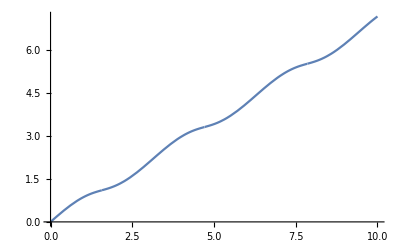

```mathematica
Plot[EllipticE[λ,0.9],{λ,0,10}]
```

```mathematica
Plot[EllipticE[JacobiAmplitude[r+5EllipticK[KZ],KZ],KZ]-EllipticE[JacobiAmplitude[r+EllipticK[KZ],KZ],KZ],{r,0,10}]
```

-Graphics-

```mathematica
DEL = 4 EllipticK[KZ]

(DEL - Log[1 - KZ^2])1/(J Z2)ϵ (a^2 J-Z2^2)
```

6.305491711078663501174066663044128682556534676

```mathematica
-66.4295227136413309692974057606307578189338801239376344987941`46.80067760995568


66.4274316490200137032445477360706676162924457636026342161207`45.00690007047743
```

```mathematica
- Log[1 - KZ^2]
```

0.000198490146461057449077888905133795099912950047

```mathematica
KZ
```

0.01408795402445775176030365017397253290871007508

```mathematica
Integrate[(JacobiSN[rr,kk])^2, rr]
```

rr/kk-JacobiEpsilon[rr,kk]/kk

```mathematica
JacobiEpsilon[0,a]
JacobiSN[0,a]
JacobiEpsilon[0,a]
EllipticE[KZ]-π/2
```

0.

0.

0.

-0.00217431333680280042433198543888457289841159

1-EllipticE[KZj]/EllipticK[KZj]